## Init

```mathematica
NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
$root = NotebookDirectory[];
SetDirectory[$root];
$FKKSRoot = "/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/";
Import[$FKKSRoot<>"Packages/HelperFunctions.wl"]
```

## QNM Evaluator

```mathematica
Import[$root<>"nonR_master.wl"]
```

## Teukolsky Evaluator

```mathematica
<<HelperFunctions.wl
<<BHEvol.m
<<VectorFieldNorm.m
<<SpinWeightedSpheroidalHarmonics.m
<<RenormalizedAngularMomentum.m
<<MSTformalism.m
<<WeylPsi4.m
<<TeukolskyT.m
<<TeuInter.wl
```

---------------------------------------------------------------------

BHEvol Functions:

KerrProcaEvolution[m-mode,n-overtone,χ (dim.-less), Procamass (initial BH mass units)]

---------------------------------------------------------------------

rstop::shdw: Symbol rstop appears in multiple contexts {VectorFieldNorm`,Global`}; definitions in context VectorFieldNorm` may shadow or be shadowed by other definitions.

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection timed out.

Connection failed.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

BBL test = {{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

Should be 0! If not, then BBL is not correct!

Imported analytic field modes.

Imported analytic Tud, Tdd and energy density.

VectorFieldNorm Functions:

VectorField[Rsol,Angsol,spin,Field-m-mode,νr,νi,Re(ω),Procamass,overtone,Normalization-mass]

FieldEnergyMomentum[AdownNorm[t,r,θ,ϕ],Procamass,spin]

---------------------------------------------------------------------

------------------------------------------------------

MSTformalism Functions:

MSTgRoots[spin,s,m,l,ω_max(max Re(ω) to which code should be evolved)]:> nureal[w] and nuimaginary[w]

MSTSolution[spin,νsol,Re(ω),Alm,s,m,l] :> RinOutpur[r] (based on irregular confluent hypergeo. functions)

------------------------------------------------------

-------------------------------------------------

WeylPsi4 Functions:

GravitationalRadiation[Binc,ω(Teu),Tlmw,Rin,χ,m(Teu),l(Teu),rstart,rstop]:> Psi4Inf[t,rstar,θ,ϕ], GWPower

GWmodes[l(GW),m(GW)] :> hlm[t,rstar]

-------------------------------------------------

---------------------------------------------------------------------

Generating analytical Teukolsky T: start.

Generating analytical Teukolsky T: done.

---------------------------------------------------------------------

TeukolskyT Functions:

TeukolskyTlmw[Tdowndown[t,r,θ,ϕ],Procamass,spin,Teu-m-mode,Teu-Re(ω),rstop,rstart,θstop,θstart]

Tlmω[r]

---------------------------------------------------------------------

```mathematica
Do[TeuCode[1,0,9/10,i,1], {i,0.3,0.3, 0.05}]//Timing
```

Data import: 
	 input mass: 0.29999999999999998889776975374843459576`25.
	 data index: 130
	 mass: 0.3`25.
	 BH Spin: 0.9`25.
	 Mode: 1
	 Overtone: 0
	 Frequency: 0.2836323604304887114412526546297144404`25.150514992000527 + 0.00004648013512127190025526778527483182`21.365026594669114*I
	 Eigenvalue: -0.39559879999905111788218886039399384992`25. - 0.000042488056168004730408113187900236390910201415677367943`25.*I

Radsol[2]: 1.75195408134492396572290398003536340299`24.309764788531524 - 0.29566605197538973494809008774749484044`23.90858816434147*I

Angsol[2]: -3.14167824063605326892800150270855602179`25.149315318673548 + 3.0090690200578942157447138213657`18.13178206897535*^-7*I

precision: 25

rplus = 1.435889894354067355223698

rstart = 1.445889894354067355223698

epsilonr = 0.006964322291925094379954

rstop = 663.6666666666667160099122

r glue = 79.64

Interpolation: Start.

rmesh = 199

Thetamesh = 49

ThetaStart = 0.007767974743979812191074785

ThetaStop = 3.135539638126066286361038

Exponential extension: Start.

Solution at horizon: Test:

Rad[rtst] = 0.91754956614814094939564 - 0.43406856444505651984784 I

Exponential extension: Done!

Generating Interpolating functions for A_μ

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 1

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 2

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

General::stop: Further output of xAct`xTensor`PrintAsCharacter::argx will be suppressed during this calculation.

Data produced for: 3

Data produced for: 4

Interpolation: Done.

Adownvector[0,2,2,2] = {-0.901396, 1.14052, -0.487886, 4.67911}

Massnormalization: Start.

Tuptdownt test = -1.08935647138605729011828771036

sqrtmg test = 3.76474079784964483565743350856

rplus = 1.435889894354067355223698

rintstart = 1.44847914847200920362979559286

epsilonrint = 0.008767562309229220612865

rintstop = 680.388571127700199071585142442

thetastart = 0.007767974743979812191074785

thetastop = 3.135539638126066286361038

massNorm obtained: 2580.19074715450

Anorm obtained: 0.0033870180952792683819

Massnormalization: Done.

FindMinimum::reged: The point {4.8681,0.} is at the edge of the search region {0.,6.28319} in coordinate 2 and the computed search direction points outside the region.

Beginning Tlmω calculation

Subscript[T, μν] test: {{3.1387890680898495*^-6, 2.524932808994803*^-6, -7.823210544937628*^-7, -8.650371818318088*^-6}, {2.524932808994803*^-6, -0.00004076381591210996, 0.000011430967912895032, -0.000013407831419837934}, {-7.823210544937628*^-7, 0.000011430967912895032, 0.000014500972574110535, 4.310542103669997*^-6}, {-8.650371818318088*^-6, -0.000013407831419837934, 4.310542103669997*^-6, 0.000040093882036141686}}

TnnExpl Test: 4.855304377600522*^-8

rrange: {1.44588989435406735522369819838596156591`25., 1.4459228608042461999511838577163665271`25., 1.44606571542168786043695504814812135893`25.} ...

θrange: {0.00776797474397981219107478523255849723`25., 0.0716000495068795361537270913018170288`25., 0.13543212426977926011637939737107556038`25.} ...

---------------------------------------------------------------------

Generating: Tnn...

Generating: Tmn...

Generating: Tmm...

Generating: Done.

---------------------------------------------------------------------

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 2.43931678118436217945959

Generating: Interpolation data...

Generating: Tlmω.

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 9.21267727394496866308932

Generating: Interpolation data...

Generating: Tlmω.

Generating: Done.

---------------------------------------------------------------------

MST Solution --------------------------------------

νsol[1]: 1.5`20. + 1.99432859529230066542027088871691375971`20.*I

1.5+0.70894327426231762423 ⅈ

0.5+0.70895546883103040295 ⅈ

2.4393167811843621795

Power::infy: Infinite expression 1/(0``-0.23434706931922658+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.23420348221868334+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.234203296270298+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

νsol = 0.5000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 + 0.7089554688310304029456605585056490421486164772342873576686403408726770583574890951161686508674719676 I

MST Solution --------------------------------------

νsol[1]: 2.5`20. + 2.30268505469030770882454817183315753937`20.*I

2.595814934577721278

2.5960657368637567661

9.2126772739449686631

νsol = 2.596065736863756766087615659956966392816822909989839324956117855953774443962197442553911305718195024

MST Solution --------------------------------------

νsol[1]: 3.5`20. + 1.948794120898588611012769433727953583`20.*I

3.7064484559408739095

3.7065570731010009595

17.499939543206425404

νsol = 3.706557073101000959462307662454499989074234885022323505895095847717056582582475659392489200638642899

GW Power --------------------------------------

Mode: {2, 2}

221.2222222222222386699707

2.445889894354067355223698

Eigenvalues of SWSH: 2.43931678118436217945959

Psi4(r->Inf): Done.

Total GW energy flux: Done.

Mode: {3, 2}

221.2222222222222386699707

2.445889894354067355223698

Eigenvalues of SWSH: 9.21267727394496866308932

Psi4(r->Inf): Done.

Total GW energy flux: Done.

{445.749,Null}

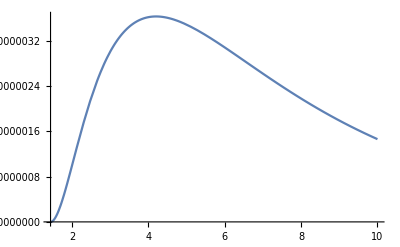

```mathematica
Plot[TeukolskyT`TnnInter[r,1]//Abs, {r,1.435,10}]
```

## Pieces of Teuk Evaluator

### Vector Field

```mathematica
<<VectorFieldNorm.m
```

```mathematica
modedataoutput=Import[ToString[$root<>"precision_mode_library/m"<>ToString[1]<>ToString["n"]<>ToString[0]<>ToString["_a"]<>ToString[900000]<>ToString["_Sm1_prec.mx"]]]//.{QNMcode`rν->rν,QNMcode`iν->iν,QNMcode`θ->θ,QNMcode`R->R}//.{QNMmode`rν->rν,QNMmode`iν->iν,QNMmode`θ->θ,QNMmode`R->R};
pos=Position[modedataoutput[[3,All]],Nearest[modedataoutput[[3,All]],0.3]//First][[1,1]];
Rsol=R/.modedataoutput[[6,pos]];
Anglsol=modedataoutput[[2,pos]];
Procamass=modedataoutput[[3,pos]];
wr=modedataoutput[[5,pos]]//Re;
wi=modedataoutput[[5,pos]]//Im;
νrv=rν/.modedataoutput[[4,pos]];
νiv=iν/.modedataoutput[[4,pos]];
parameters={χ->0.9,m->1,νr->νrv,νi->νiv,ωi->0,iν->νiv, rν->νrv,ωr->wr,μ->Procamass,nh->0};
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};
Sangl[θθ_]:=Anglsol//.coordinates//.{θ->θθ};
dSangltemp=D[Sangl[θ],θ];
dSangl[θθ1_]:=dSangltemp//.{θ->θθ1};
ddSangltemp=D[dSangl[θ],θ];
ddSangl[θθ2_]:=ddSangltemp//.{θ->θθ2};
With[{Rad=Rsol, dRad = Derivative[1][Rsol], ddRad = Derivative[2][Rsol]},
solidentify={Ri[r_]:>Im[Rad[r]],Rr[r_]:>Re[Rad[r]],Ri'[r_]:>Im[dRad[r]],Rr'[r_]:>Re[dRad[r]],Rr''[r_]:>Re[ddRad[r]],Ri''[r_]:>Im[ddRad[r]],Si[θ_]:>Im[Sangl[θ]],Sr[θ_]:>Re[Sangl[θ]],Si'[θ_]:>Im[dSangl[θ]],Sr'[θ_]:>Re[dSangl[θ]],Sr''[θ_]:>Re[ddSangl[θ]],Si''[θ_]:>Im[ddSangl[θ]]};
];

(*VectorField[Rsol, Anglsol, 0.9,1,0,νrv,νiv,wr,0.3,1]*)
```

```mathematica
$FKKSRoot = "/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/";
MySolution = getResults[$FKKSRoot<>"Solutions/", {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[0.3], InputForm], "/"->"_"]}}]//First;
Import[$FKKSRoot<>"Packages/xActSetup.wl"]
Import[$FKKSRoot<>"Packages/EnergyMomentum.wl"]
Block[{νi,νr},Aupmine = Import[$FKKSRoot<>"Expressions/AuprealComponents.mx"]/.ToParamSymbols//FromxActVariables;]
myup$=FKKSProca[MySolution, Optimized->True, QuasiboundState->True];
mydown$ = {tt,rr,thth,phph}|->(Table[myup$[t,r,θ,ϕ][{i,-sphericalchart}], {i,0,3}]//FromxActVariables)/.t->tt/.r->rr/.θ->thth/.ϕ->phph//ApplyRealSolutionSet[MySolution];

AdownSimp=Import[Global`$root<>"Expressions/AdownSimp.mx"]//.coordinates;
AupSimp=Import[Global`$root<>"Expressions/AupSimp.mx"]//.coordinates;
nildown$$ = {t, r,θ,ϕ}|->AdownSimp/.parameters/.solidentify/.Private`t->t/.Private`r->r/.Private`θ->θ/.Private`ϕ->ϕ//Evaluate;
nilup$$ = {t, r,θ,ϕ}|->AupSimp/.parameters/.solidentify/.Private`t->t/.Private`r->r/.Private`θ->θ/.Private`ϕ->ϕ//Evaluate;
```

```mathematica
With[{T=0,R=2,Θ=2,Φ=2},
Row[{Column[{
Row[{"nildown$$            ",#}]&@nildown$$[T,R,Θ,Φ],
Row[{"Private`Adownvector  ",#}]&@Private`Adownvector[T,R,Θ,Φ],
Row[{"mydown$              ",#}]&@mydown$[T,R,Θ,Φ]}],Spacer[20],
Column[{
Row[{"nilup$$            ",#}]&@nilup$$[T,R,Θ,Φ],
Row[{"Private`Aupvector  ",#}]&@Private`Aupvector[T,R,Θ,Φ],
Row[{"myup$              ",#}]&@myup$[T,R,Θ,Φ][[1]]
}]
}]
]
```

```mathematica
Import[$FKKSRoot<>"Packages/EnergyMomentum.wl"]
mytoten = FKKSNormalization[MySolution,1, Recalculate->True]
```

```mathematica
mytoten["Normalization"]*mydown$[0,2,2,2]
TeuInterEnv`AdownNorm[0,2,2,2]
```